# A Yatzy Variant

## Författare

Stefan Josefsson, stejos@kth.se
Joe Huldén, joeda@kth.se

## Summering

Sannolikheterna för händelserna samt väntevärde för ett kast 
p(Par): 275/576
p(Två par): 413/5760
p(Triss): 191/2880
p(Kåk): 31/5760
p(Fyrtal): 1/240
p(Stege): 3/640

Väntevärdet: 1563177/160000

## Grafer

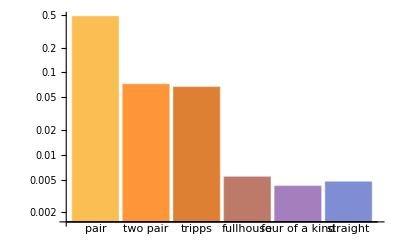

## Kod

```mathematica
ClearAll["`*"]
(*1.Specifiera grundmängden.*)
n =20;
s0 = Tuples[{Range[1,4],Range[1,6],Range[1,8],Range[1,12],Range[1,20]}];
s2 = Tuples[{Range[1,4],Range[1,6],Range[1,8],Range[1,12],Range[1,20]}];
Length [s0]
4*6*8*12*20

(*Sorteringen för grundmängden.*)
nTot = Length[s0];
t[s_]:=Sort[s - Min[s]];
s2 = Sort/@s2;
s0=t/@s0;

(*Pattern matching*)
aPair[{___,x_,x_,___}]:=True
aPair[{___}]:=False
twoPair[{___,x_,x_,___,y_,y_,___}/; x≠y]:=True
twoPair[{___}]:=False
tripps[{___,x_,x_,x_,___}]:=True
tripps[{___}]:=False

fullhouse[{x_,x_,y_,y_,y_} /;x≠y] :=True
fullhouse[{y_,y_,y_,x_,x_}/;x≠y] := True
fullhouse[{___}]:=False
fourOfAKind[{___,x_,x_,x_,x_,___}]:=True
fourOfAKind[{___}]:=False
straight[{0,1,2,3,4}]:=True
straight[{___}]:=False

(*Funktion för antalet gynnsamma utfall för varje pokerhand.*)
fourOfAKindVal[x_]:=Count[fourOfAKind/@x,True]
fullHouseVal[x_]:=Count[fullhouse/@x,True]
trippsVal[x_]:=(Count[tripps/@x,True] - fourOfAKindVal[x] - fullHouseVal[x])
twoPairVal[x_]:=(Count[twoPair/@x,True] - fullHouseVal[x])
pairVal[x_]:=(Count[aPair/@x,True] - twoPairVal[x] - trippsVal[x] - fourOfAKindVal[x] - fullHouseVal[x]) 
straighVal[x_]:=Count[straight/@x,True]

(*Sannolikheten räknas fram här: gynnsamma_utfall/grundmängden(totala utfallsrum).*)
p1 = pairVal[s0] /nTot
p2 = twoPairVal[s0]/nTot
p3 = trippsVal[s0]/nTot
p4 = fullHouseVal[s0] /nTot
p5 =fourOfAKindVal[s0]/nTot
p6 =straighVal[s0]/nTot

BarChart[{{p1,p2,p3,p4,p5,p6}},ChartLabels->{"pair","two pair","tripps", "fullhouse", "four of a kind", "straight"},ScalingFunctions->"Log"]
```

46080

46080

275/576

413/5760

191/2880

31/5760

1/240

3/640

-Graphics-

```mathematica
(*Väntevärdet*)
aPairV[{___,x_,x_,___}]:=2*x
aPairV[{___,x_,x_,x_,___}]:=0
aPairV[{___,y_,y_,___,x_,x_,___}]:=0
aPairV[{___}]:=0

twoPairV[{x_,x_,x_,y_,y_}]:=0
twoPairV[{x_,x_,y_,y_,y_}]:=0
twoPairV[{___,x_,x_,___,y_,y_,___}/; x≠y]:=2*x + 2*y
twoPairV[{___}]:=0

trippsV[{___,x_,x_,x_,x_,___}]:=0
trippsV[{x_,x_,x_,y_,y_}]:=0
trippsV[{x_,x_,y_,y_,y_}]:=0
trippsV[{___,x_,x_,x_,___}]:= 3*x
trippsV[{___}]:=0

fullhouseV[{x_,x_,y_,y_,y_} /;x≠y] :=2*x+3*y
fullhouseV[{y_,y_,y_,x_,x_}/;x≠y] := 3*y +2*x
fullhouseV[{___}]:=0

fourOfAKindV[{___,x_,x_,x_,x_,___}]:=4*x
fourOfAKindV[{___}]:=0

straightV[{x1_, x2_,x3_,x4_,x5_}]/;Differences[{x1,x2,x3,x4,x5}]=={1,1,1,1}:=x1+x2+x3+x4+x5
straightV[{___}]:=0

(*Väntevärdet för ett spel.*)
a1 = Total[aPairV/@s2] /pairVal[s1] *p1
a2 = Total[twoPairV/@s2]/twoPairVal[s1] * p2
a3 = Total[trippsV/@s2]/trippsVal[s1] * p3
a4 = Total[fullhouseV/@s2]/fullHouseVal[s1] *p4
a5 = Total[fourOfAKindV/@s2] /fourOfAKindVal[s1] *p5
a6 = Total[straightV/@s2]/straighVal[s1] * p6
a1+a2+a3+a4+a5+a6
```

61047/8000

10773/8000

10773/16000

399/6400

63/2500

63/2000

1563177/160000